```mathematica
a[e_]:=6.67*10^-11 * 5.97 * 10^24 / (e+6370000)^2
```

```mathematica
(a[8848]-9.8)/a[8848]
```

-0.00140653

```mathematica
(9.793922-9.83366)/9.81
```

-0.00405076

```mathematica
data=Import["http://www.cs.utexas.edu/~evanott/PHY110C_Textbook/static/data_analysis/_downloads/assignment3data.csv"];
```

```mathematica
halley=data[[All,31;;33]];
```

```mathematica
ListPointPlot3D[halley-sun]
```

-Graphics3D-

```mathematica
sun = data[[All,1;;3]];
```

```mathematica
halley[[1]]
```

{8.8353×10^10,0.,0.}

```mathematica
halley2d=Import["http://www.cs.utexas.edu/~evanott/PHY110C_Textbook/static/data_analysis/_downloads/halley_data.csv"];
```

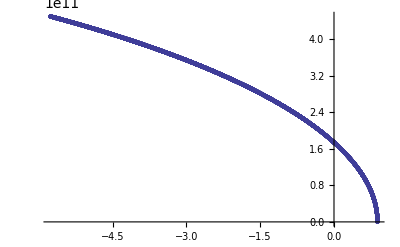

```mathematica
ListPlot[halley2d]
```

```mathematica
Needs["PlotLegends`"];
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

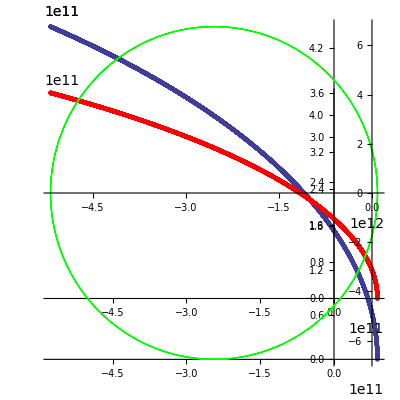

```mathematica
plotFit[halley2d_]:=Module[{thetaList, rList,thetaRList,c,e,theta,fit},
thetaList=Mod[ArcTan[halley2d[[All,2]]/halley2d[[All,1]]]+2Pi,Pi];
rList=Sqrt[halley2d[[All,1]]^2+halley2d[[All,2]]^2];
thetaRList=Table[{thetaList[[i]],rList[[i]]},{i,1,Length[halley2d]}];
fn[theta_]:=c/(1+e Cos[theta]);
fit=FindFit[thetaRList[[1;;14924]],fn[theta],{c,e},{theta}];

Show[
ListPolarPlot[Transpose[{thetaList,rList}],
PlotStyle->PointSize[Large]],
ListPlot[halley2d,PlotStyle->Directive[Red,PointSize[Small]]],
PolarPlot[fn[theta]/.fit,
{theta,0,4Pi},
PlotStyle->Green],
PlotRange->{-10^12,1 10^12}]
]
plotFit[halley2d]
```

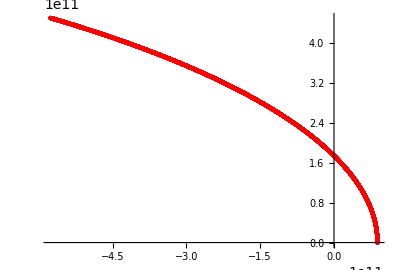

```mathematica
Show[ListPolarPlot[thetaRList,PlotStyle->PointSize[Large]],ListPlot[halley2d,PlotStyle->Directive[Red,PointSize[Small]]]]
```

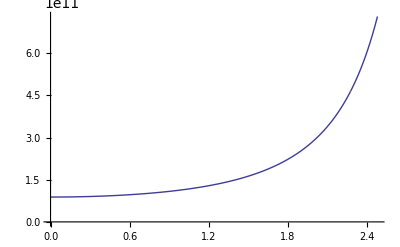

```mathematica
ListPlot[%685,Joined->True]
```

```mathematica
Length[thetaRList]
```

14924

```mathematica
FindFit[thetaRList[[1;;14924]],c/(1+e Cos[theta]),{c,e},{theta}]
```

{c→1.73727×10^11,e→0.966439}

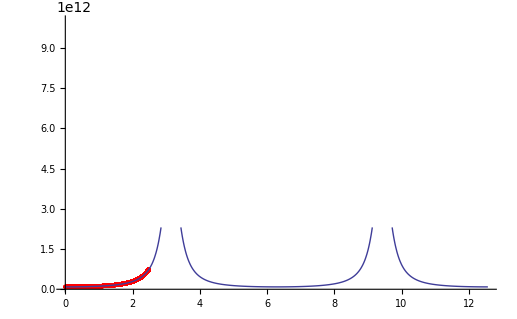

```mathematica
Show[ListPlot[thetaRList,PlotStyle->Red],Plot[c/(1+e Cos[theta])/.{c->1.7372705457425507*^11,e->0.9664392262159686},{theta,0,4Pi}],PlotRange->{{0,4Pi},{10^11,10^13}}]
```

```mathematica
fitted[theta_]:=c/(1+e Cos[theta])/.{c->1.7372705457425507*^11,e->0.9664392262159686}
```

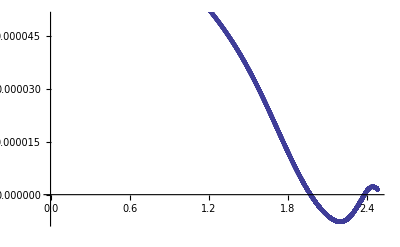

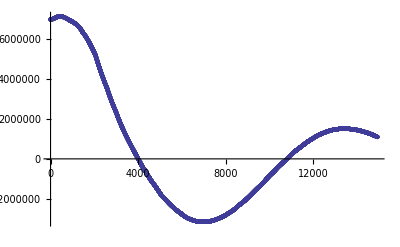

```mathematica
resid = Table[{thetaRList[[i,1]],(thetaRList[[i,2]]-fitted[thetaRList[[i,1]]])/thetaRList[[i,2]]},{i,1,Length[thetaRList]}];
ListPlot[resid]
```

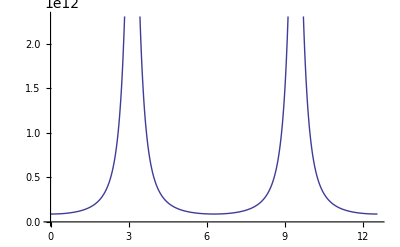

```mathematica
Plot[c/(1+e Cos[theta])/.{c->1.7372705457425507*^11,e->0.9664392262159686},{theta,0,4Pi}]
```

```mathematica
μ=2.2*10^14 * 1.989*10^30/(1.989*10^30+2.2*10^14)
```

2.2×10^14

```mathematica
γ=6.67*10^-11*2.2*10^14 * 1.989*10^30
```

2.91866×10^34

```mathematica
l=Sqrt[γ μ c]
```

1.05618×10^30

```mathematica
e=0.9664392262159686
```

0.966439

```mathematica
c=1.7372705457425507*^11
```

1.73727×10^11

```mathematica
a=c/(1-e^2)
```

2.63242×10^12

```mathematica
2 Pi Sqrt[a^3/(6.67*10^-11 * 1.989*10^30)]/(3600 * 24 * 365.25)
```

73.8292

```mathematica
halley2d
```

{{8.8353×10^10,0.},{8.83529×10^10,1.33812×10^8},{8.83528×10^10,2.67623×10^8},«14918»,{-5.76079×10^11,4.49136×10^11},{-5.76112×10^11,4.49146×10^11},{-5.76146×10^11,4.49155×10^11}}

```mathematica
Export["C:/Users/Evan/GitProjects/runestone/data_analysis/_sources/Assignments/halley_data.csv",halley2d]
```

C:/Users/Evan/GitProjects/runestone/data_analysis/_sources/Assignments/halley_data.csv

```mathematica
thetaRList[[1;;5]]
```

{{0.,8.8353×10^10},{0.00151451,8.8353×10^10},{0.00302902,8.83532×10^10},{0.00454352,8.83534×10^10},{0.00605799,8.83538×10^10}}

```mathematica
sunP=Table[Sqrt[(sun[[i+1,1]]-sun[[i,1]])^2+(sun[[i+1,2]]-sun[[i,2]])^2+(sun[[i+1,3]]-sun[[i,3]])^2],{i,1,Length[sun]-1}]
```

{2.46192×10^6,2.46192×10^6,2.46191×10^6,2.46189×10^6,2.46187×10^6,2.46183×10^6,2.46179×10^6,2.46173×10^6,2.46167×10^6,2.4616×10^6,2.46152×10^6,2.46144×10^6,2.46134×10^6,2.46124×10^6,2.46113×10^6,2.46101×10^6,2.46088×10^6,2.46074×10^6,«14887»,1.9417×10^6,1.9423×10^6,1.9429×10^6,1.94351×10^6,1.94411×10^6,1.94472×10^6,1.94533×10^6,1.94595×10^6,1.94656×10^6,1.94718×10^6,1.9478×10^6,1.94842×10^6,1.94905×10^6,1.94967×10^6,1.9503×10^6,1.95094×10^6,1.95157×10^6,1.95221×10^6}

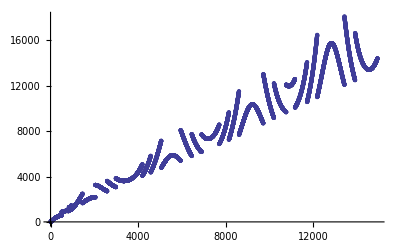

```mathematica
ListPlot[Table[Sqrt[(sun[[i+1,1]]-sun[[i,1]])^2+(sun[[i+1,2]]-sun[[i,2]])^2],{i,1,Length[sun]-1}]]
```